```mathematica
f1[x_]:=(Abs[x-Pi/2]+Pi/2)^2+0.8*E^(-5*Abs[x-Pi/2]);
f2[x_]:=(-Abs[x-Pi/2]+Pi/2)^2-0.8*E^(-5*Abs[x-Pi/2]);
```

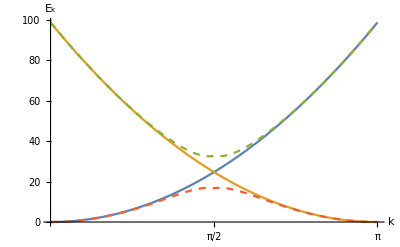

```mathematica
Plot[{10*x^2,10*(x-Pi)^2,10*f1[x],10*f2[x]},{x,0,Pi},PlotStyle->{Automatic,Automatic,Dashed,Dashed}, AxesLabel->{"k","E_k"},LabelStyle->{FontSize->14},Ticks->{{Pi/2,Pi},None}]
```